```mathematica
PacletFind/@{"Wolfram/DiagrammaticComputation","WolframInstitute/Hypergraph","Wolfram/Lambda"}
```

{{},{},{}}

```mathematica
Map[
PacletInstall[#,ForceVersionInstall->True]&,{"https://wolfr.am/DiagrammaticComputation.paclet","https://wolfr.am/Hypergraph.paclet","https://wolfr.am/Lambda.paclet"}]
```

{PacletObject[…],PacletObject[…],PacletObject[…]}

```mathematica
<<Wolfram`DiagrammaticComputation`
```

```mathematica
Diagram[DiagramRightComposition[DiagramProduct[Diagram[C,p],DiagramComposition[Diagram[B,p,{p,p}],Diagram[B,p,{p,p}]]],DiagramComposition[Diagram[A,{p,p},p],DiagramProduct[Diagram[A,{p,p},p],IdentityDiagram[p]]],Diagram[D,p,p]]]
```

-Graphics-

#### Rewriting

```mathematica
<<Wolfram`Lambda`
```

```mathematica
NestList[
DiagramReplace[Values[$LambdaInteractionRules]],
LambdaInteractionNet[λ[λ[1[2]][1]][λ[1]]],
5
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LambdaInteractionNet[BetaReduce@TagLambda@λ[λ[1[2]][1]][λ[1]]]
```

-Graphics-

#### Trees and Graphs to Grids

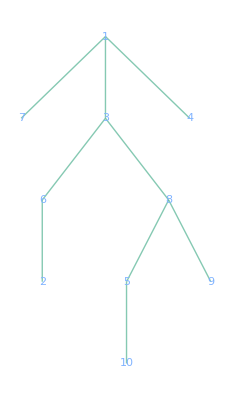
```mathematica
DiagramGrid[ToDiagram[-Graphics-],Dividers->All,"Arrange"->False,"Wires"->False,"PortLabels"->None,"PortArrows"->None,"Style"->Directive[EdgeForm[None],FaceForm[None]]]
```

-Graphics-

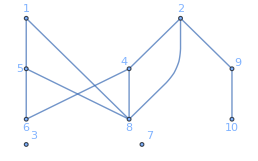
```mathematica
DiagramGrid[ToDiagram[-Graphics-],Dividers->All,"Arrange"->False,"Wires"->False,"PortLabels"->None,"PortArrows"->None,"Style"->Directive[EdgeForm[None],FaceForm[None]]]
```

-Graphics-